```mathematica
SetDirectory[NotebookDirectory[]];
```

{{24,211.457,161.289},{32,169.142,143.868},{40,129.786,103.663},{48,114.538,90.0792},{56,100.431,77.4456},{64,87.497,73.2587},{72,75.106,55.6766},{80,73.178,55.6766},{88,71.24,59.4666},{96,59.412,51.4047},{112,57.594,50.5447},{128,43.733,35.4712}}

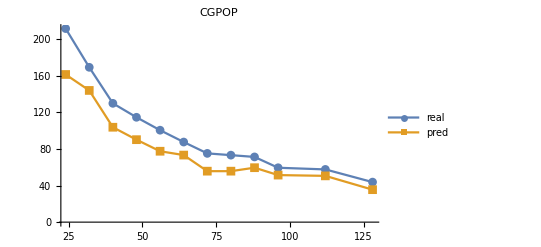

allTime/cgpop.pdf

```mathematica
bt = Import["allTime/cgpop.txt","Table"]
a = ListLinePlot[{Transpose[{bt[[;;,1]],bt[[;;,2]]}],Transpose[{bt[[;;,1]],bt[[;;,3]]}]},PlotMarkers->Automatic,PlotLabel->"CGPOP",PlotLegends->{"real","pred"}]
Export["allTime/cgpop.pdf",a]
```